# Initialization

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"];
Needs["ErrorListLinePlot`"];
```

Get::noopen: Cannot open ErrorListLinePlot`.

Needs::nocont: Context ErrorListLinePlot` was not created when Needs was evaluated.

# Functions

### ImgCoord2DataCoord (integer)

```mathematica
Img2DataCoord[imageSize_,coordinate_]:=Module[{},
{#⟦2⟧,#⟦1⟧}&@Abs@({0,imageSize⟦2⟧+1}-Ceiling@coordinate)
]
```

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### MyThresholding

```mathematica
MyThresholding[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue.dat"),thblue=<<(analysisFolder<>"_thblue.dat");ToString@thblue<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,
"Blue Threshold : "<>flagBlue},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myImg⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];
If[color==3,thblue={threshold1,threshold2};flagBlue=ToString@thblue<>"Saved";thblue>>analysisFolder<>"_thblue.dat"];
],
Spacer@5,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];If[color==3&&ValueQ@thblue,{threshold1,threshold2}=thblue]],
ControlPlacement->Left
]
]]
```

```mathematica
MyThresholding3D[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue3D},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D.dat"),thblue3D=<<(analysisFolder<>"_thblue3D.dat");ToString@thblue3D<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦frame,z⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
(*"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,*)
"Blue Threshold 3D : "<>flagBlue3D},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
(*If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];*)
(*If[color==3,*)thblue3D={threshold1,threshold2};flagBlue3D=ToString@thblue3D<>"  Saved";thblue3D>>analysisFolder<>"_thblue3D.dat"(*]*);
],
Spacer@5,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];*)If[(*color==3&&*)ValueQ@thblue3D,{threshold1,threshold2}=thblue3D]],
ControlPlacement->Left
]
]]
```

### MyBinarization

```mathematica
MyBinarization[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue,max,imga,imgb,color,frame,threshold,lowpass,hipass,lo,hi,myOutline,myFill},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue2.dat"),thblueAll=<<(analysisFolder<>"_thblue2.dat");Append[ToString/@thblueAll,"Already Saved"],{"Not Yet Determined"}];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[
imga=ImageAdjust[myImg⟦color,frame⟧, {0, 0, 1},threshold1⟦color⟧];
max=BandPass[ImageMultiply[ImageAdjust[myImg⟦color,1⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=SelectComponents[ImageMultiply[Binarize[BandPass[imga,{lowpass,hipass}],max threshold],mask],"Count",lo<#<hi&];
Column@{GraphicsRow[{Show[If[myOutline==True&&myFill==False,{imga,Graphics[{Green,#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2⟧},If[myFill==True,{imga,Graphics[{Green,Polygon@#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2,1,1⟧},imga]]],imgb},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],
Prepend[flagBlue,"Blue Threshold 2  :"]}},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Row@{"Display options: ",Spacer@5,"outline ",Checkbox[Dynamic@myOutline],Spacer@10,"filled ",Checkbox[Dynamic@myFill]},
Spacer@10,
Button["Save Threshold 2",
If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];
If[color==3,thblueAll={mymaxblue=max,thblue2=threshold,bandpassblue={lowpass,hipass},dotsizeblue={lo,hi}};
flagBlue=Append[ToString/@thblueAll,"Saved"];
thblueAll>>analysisFolder<>"_thblue2.dat"];
],
Spacer@10,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];If[color==3&&ValueQ@thblueAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblueAll]]
]]]
```

```mathematica
MyBinarization3D[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue3D,max,imgb,color,frame,threshold,lowpass,hipass,lo,hi},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D2.dat"),thblue3DAll=<<(analysisFolder<>"_thblue3D2.dat");Append[ToString/@thblue3DAll,"  Already Saved"],{"Not Yet Determined"}];
color=1;
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[max=BandPass[ImageMultiply[ImageAdjust[myImg⟦1,Round@(Length@myImg⟦1⟧/2)⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[ImageAdjust[myImg⟦frame,z⟧ , {0, 0, 1}, threshold1⟦color⟧],{lowpass,hipass}];
Column@{GraphicsRow[{ImageAdjust[myImg⟦frame,z⟧, {0, 0, 1},threshold1⟦color⟧],
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mask],"Count",lo<#<hi&]},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
(*Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],*)
Prepend[flagBlue3D,"Blue Threshold 3D 2  :"]}},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Button["Save Threshold 3D 2",
(*If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];*)
(*If[color==3,*)thblue3DAll={mymaxblue3D=max,thblue3D2=threshold,bandpassblue3D={lowpass,hipass},dotsizeblue3D={lo,hi}};
flagBlue3D=Append[ToString/@thblue3DAll,"  Saved"];
thblue3DAll>>analysisFolder<>"_thblue3D2.dat"(*];*)
],
Spacer@10,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];*)If[(*color==3&&*)ValueQ@thblue3DAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblue3DAll]]
]]]
```

### FindParticles

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],"Count",small<#<large&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticles[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,compResults},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&];
compResults=ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
compResults⟦All,2⟧
]
```

```mathematica
(* After finding particles, add track number as 0, and add frame number *)
MyParticleFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
result=FindParticles[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧;
result=Table[Thread@{i,result⟦i⟧},{i,1,Length@result,1}];
result=Prepend[#,0]&/@#&/@result
]
```

```mathematica
FindGranuleMasks[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&]
]
```

```mathematica
myGranuleMaskFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
FindGranuleMasks[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input does not have color code such as {1,0,0} for red *)
ParticleFitting2[myColMovie_,channel_,mylongtracks_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
myTrimSize=2*pad+1;
Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitter[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitterFixedSigma[myColMovie_,channel_,mySpots_,pad_,avgFrameN_,sigma_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;

myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
ParticleFitting3[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;

Table[
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[mySpots⟦frame,spot,2⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,frame+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,Length@Flatten@track1⟦1⟧]&; 
t2=track2//Flatten//Partition[#,Length@Flatten@track2⟦1⟧]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
t1⟦All,{1,2}⟧=t1⟦All,{2,1}⟧;
t2⟦All,{1,2}⟧=t2⟦All,{2,1}⟧;
ol={t1,t2}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### NearestNeighborLinking

```mathematica
(* Using a globally determined (automatic) threshod for binarization *)
NearestNeighborLinking1[img_,channel_,startFrame_,startPosition_,pad_,bandpass_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust@myTrimImg,bandpass]],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
(* Using user defined threshod for binarization *)
NearestNeighborLinking2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
NearestNeighborLinking3D2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

### ClickAndTrack

```mathematica
ClickAndTrack[imgRaw_,img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTruckNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];],
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames["*_myTrack_"<>myColor<>"*",DirectoryName@analysisFolder];
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

```mathematica
ClickAndTrack3D[(*imgRaw_,*)img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{(*"_thred2.dat","_thgreen2.dat",*)"_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTruckNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];](*,
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames["*_myTrack_"<>myColor<>"*",DirectoryName@analysisFolder];
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

### FilterFitOutlier

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma *)
FilterFitOutlier[mySpotsFit_,maxDxy_,maxSig_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxSigX=Position[mySpotsFit⟦All,All,4,3,1⟧,x_/;Abs@x>maxSig];
idxSigY=Position[mySpotsFit⟦All,All,4,3,2⟧,x_/;Abs@x>maxSig];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[mySpotsFit,idxOutliers]
]
```

### SpotLocationOnCell

```mathematica
(* function to show cell movie with tracked spot positions *)
SpotLocationOnCell[myColMovie_,thred_,redSpots_,thgreen_,greenSpots_,thblue_,blueSpots_]:=Module[{th,colCircle,spots},
Manipulate[If[color==1,th=thred;colCircle=Red;spots=redSpots,
If[color==2,th=thgreen;colCircle=Green;spots=greenSpots,
th=thblue;colCircle=Blue;spots=blueSpots]];
Show[ImageAdjust[myColMovie⟦color,frame⟧,{0,0,1},th],Graphics[{colCircle,Circle[#,7]}&/@spots⟦frame⟧]],{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myColMovie⟦1⟧,1},ControlType->{RadioButtonBar,Automatic}]
]
```

### ShiftingDataPoints

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMin[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
myStart=(#-Min@#)+1&@Round@(10*myOffset);
myDataResample=Table[myDataInterpol⟦i,myStart⟦i⟧;;⟧,{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[myDataResample⟦i⟧,ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMean[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
(*myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;*)
myDataInterpol=Table[Array[myDataInterpolFunc⟦i⟧,1+myResolution*(Length@myData⟦i⟧-1),{1,Length@myData⟦i⟧}],{i,1,Length@myData,1}];
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset);
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[{myDataResample⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
myAllBlueNum
```

myAllBlueNum

```mathematica
ShiftingDataPointsMin[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
ShiftingDataPointsMean[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
test=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myData=myAllBlueNum;
```

```mathematica
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
```

```mathematica
myDataInterpol=Array[#,1+10*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
```

```mathematica
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
```

```mathematica
test=myDataResample⟦All,;;All;;10⟧
```

{}

```mathematica
myFillSize=Max@#-#&@(Length/@test)
```

{}

```mathematica
myDataResample=Table[Flatten[Append[{test⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@test,1}]
```

{}

```mathematica
ConstantArray[{},]
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},Null].

ConstantArray[{},Null]

```mathematica
Flatten[Append[{test⟦10⟧},ConstantArray[{},myFillSize⟦10⟧]],1]
```

Part::partw: Part 10 of {} does not exist.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},{}⟦10⟧].

{{}⟦10⟧,ConstantArray[{},{}⟦10⟧]}

```mathematica
myDataResample⟦10⟧
```

Part::partw: Part 10 of {} does not exist.

{}⟦10⟧

### MyCropMaker

```mathematica
MyCropMaker[myColMovie_,myRNAtracks_,pad_,analysisFolder_]:=Module[{myTfFunc,avgFrameN,myCrops,tempTime,tempCenter,tempCenterColReg,tempRed,tempGreen,tempBlue,myCropsAvg},
myTfFunc=<<(FileNames["TransformationFunction.m",ParentDirectory@DirectoryName@analysisFolder]⟦1⟧);
avgFrameN=<<(FileNames["*avgFrameN*",DirectoryName@analysisFolder]⟦1⟧);
myCrops=
	Table[
		Table[
		tempTime=myRNAtracks⟦track,frame,2⟧;
		tempCenter=Ceiling[myRNAtracks⟦track,frame,3,1⟧];
		tempCenterColReg=Ceiling[myTfFunc@myRNAtracks⟦track,frame,3,1⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myRNAtracks⟦track⟧,1}],
	{track,1,Length@myRNAtracks,1}];
myCrops>>analysisFolder<>"_Crops.m";
myCropsAvg=Mean/@#&/@Transpose/@myCrops;
myCropsAvg>>analysisFolder<>"_Crops_AVG.m";
{myCrops,myCropsAvg}]
```

### MyAutoCategorization

```mathematica
MyAutoCategorization[myCropsAvg_,myRNAtracks_,lowpass_,highpass_]:=Module[{myCropsAvgBandPass,myCropsAvgBinari,myCropsAvgBinariSort,myCropsAvgBinariData,myCropsAvgBinariDataDigital,idx1,idx2,idx3,idx4,idx,myAvgCropsCategorized,myRNAtracksCategorized},
myCropsAvgBandPass=BandPass[#,{lowpass,highpass}]&/@#&/@myCropsAvg;
myCropsAvgBinari=Binarize/@#&/@myCropsAvgBandPass;
myCropsAvgBinariSort=SelectComponents[#,#AdjacentBorderCount==0&&#Count >3&]&/@#&/@myCropsAvgBinari;
myCropsAvgBinariData=Flatten[ComponentMeasurements[#,"Count"]&/@#&/@myCropsAvgBinariSort,1];
myCropsAvgBinariData⟦Position[myCropsAvgBinariData,{}]//Flatten⟧={0->0};
myCropsAvgBinariDataDigital=Partition[Total/@myCropsAvgBinariData⟦All,All,2⟧,3];
myCropsAvgBinariDataDigital=Thread@{Range@Length@#,#}&@myCropsAvgBinariDataDigital⟦All,{2,3}⟧;
idx1=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧==0&&x⟦2,2⟧==0])⟦All,1⟧;
idx2=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧>0&&x⟦2,2⟧==0])⟦All,1⟧;
idx3=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧==0&&x⟦2,2⟧>0])⟦All,1⟧;
idx4=(Cases[myCropsAvgBinariDataDigital,x_/;x⟦2,1⟧>0&&x⟦2,2⟧>0])⟦All,1⟧;
idx={idx1,idx2,idx3,idx4};
myAvgCropsCategorized=ImageAdjust/@#&/@#&/@Table[myCropsAvg⟦idx⟦i⟧⟧,{i,1,4,1}];
myRNAtracksCategorized=Table[myRNAtracks⟦idx⟦i⟧⟧,{i,1,4,1}];
{myAvgCropsCategorized,myRNAtracksCategorized}
]
```

### MyCategoryHandChecker

```mathematica
MyCategoryHandChecker[myAvgCropsCategorized_,myRNAtracksCategorized_]:=Module[{myTFidx,myIdx,myIdxSplit},
myTFidx={{True,False,False},{True,True,False},{True,False,True},{True,True,True}};
myIdx=Flatten[Table[ConstantArray[myTFidx⟦color⟧,Length@myAvgCropsCategorized⟦color⟧],{color,1,Length@myAvgCropsCategorized,1}],1];
myIdxSplit=Thread@{Prepend[#⟦;;3⟧+1,1],#}&@Accumulate@(Length/@myAvgCropsCategorized);
DynamicModule[{myDynamicIdx,myDynamicIdxSplit,myIdxNomore},
myDynamicIdx=myIdx;
Column@{Grid@Prepend[Flatten[#,1]&/@Thread@{Table["Spot "<>ToString@spot,{spot,1,Length@myIdx,1}],Flatten[myAvgCropsCategorized,1],Partition[Checkbox/@ToExpression/@Flatten@Table[Table["Dynamic@myDynamicIdx⟦"<>ToString@spot<>","<>ToString@color<>"⟧",{color,1,3,1}],{spot,1,Length@myDynamicIdx,1}],3]},{"","R","G","B","R","G","B"}],
Button["Done Checking!",
myDynamicIdxSplit=Table[myDynamicIdx⟦myIdxSplit⟦color,1⟧;;myIdxSplit⟦color,2⟧⟧,{color,1,Length@myIdxSplit,1}];
myRNAtracksHC=Table[myRNAtracksCategorized⟦color,Flatten@Position[#==myTFidx⟦color⟧&/@myDynamicIdxSplit⟦color⟧,True]⟧,{color,1,4,1}];
myAvgCropsHC=Table[myAvgCropsCategorized⟦color,Flatten@Position[#==myTFidx⟦color⟧&/@myDynamicIdxSplit⟦color⟧,True]⟧,{color,1,4,1}];
myIdxNomore=Table[Flatten@Position[#==myTFidx⟦color⟧&/@myDynamicIdxSplit⟦color⟧,False],{color,1,Length@myDynamicIdxSplit,1}];
Table[
Table[
Table[If[myDynamicIdxSplit⟦color,spot⟧==myTFidx⟦j⟧,myRNAtracksHC⟦j⟧=Append[myRNAtracksHC⟦j⟧,myRNAtracksCategorized⟦color,spot⟧];myAvgCropsHC⟦j⟧=Append[myAvgCropsHC⟦j⟧,myAvgCropsCategorized⟦color,spot⟧];
]
,{j,1,Length@myTFidx,1}]
,{spot,myIdxNomore⟦color⟧}],
{color,1,4,1}];
myAvgCropsHC=Table[Last/@SortBy[Flatten[#,1]&/@Thread@{myRNAtracksHC⟦color⟧,{#}&/@myAvgCropsHC⟦color⟧},First],{color,1,4,1}];
myRNAtracksHC=SortBy[#,First]&/@myRNAtracksHC;
myRNAtracksHC>>analysisFolder<>"_myRNAtracksHC.m";
myAvgCropsHC>>analysisFolder<>"_myAvgCropsHC.m";]}]]
```

### MyCategorizedTrackFitter

```mathematica
MyCategorizedTrackFitter[myRNAtracksHC_,myColMovie_,analysisFolder_,sigma_]:=Module[{myRNAtracksHCColReg,myTfFunc,avgFrameN},
myRNAtracksHCColReg=myRNAtracksHC;
myTfFunc=<<(ParentDirectory@DirectoryName@analysisFolder<>"\\TransformationFunction.m");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myRNAtracksHCColReg⟦All,All,All,3,1⟧=myTfFunc/@#&/@#&/@myRNAtracksHC⟦All,All,All,3,1⟧;

{myRedfitsR,myRedCroppedDataR,myRedCentersR}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦1⟧,5,avgFrameN,sigma];
myRedfitsR>>analysisFolder<>"myRedfitsR.m";

{myRedfitsY,myRedCroppedDataY,myRedCentersY}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦2⟧,5,avgFrameN,sigma];
myRedfitsY>>analysisFolder<>"myRedfitsY.m";

{myRedfitsP,myRedCroppedDataP,myRedCentersP}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦3⟧,5,avgFrameN,sigma];
myRedfitsP>>analysisFolder<>"myRedfitsP.m";

{myRedfitsW,myRedCroppedDataW,myRedCentersW}=MyParticleFitterFixedSigma[myColMovie,1,myRNAtracksHC⟦4⟧,5,avgFrameN,sigma];
myRedfitsW>>analysisFolder<>"myRedfitsW.m";

{myGreenfitsY,myGreenCroppedDataY,myGreenCentersY}=MyParticleFitterFixedSigma[myColMovie,2,myRNAtracksHCColReg⟦2⟧,5,avgFrameN,sigma];
myGreenfitsY>>analysisFolder<>"myGreenfitsY.m";

{myGreenfitsW,myGreenCroppedDataW,myGreenCentersW}=MyParticleFitterFixedSigma[myColMovie,2,myRNAtracksHCColReg⟦4⟧,5,avgFrameN,sigma];
myGreenfitsW>>analysisFolder<>"myGreenfitsW.m";

{myBluefitsP,myBlueCroppedDataP,myBlueCentersP}=MyParticleFitterFixedSigma[myColMovie,3,myRNAtracksHCColReg⟦3⟧,5,avgFrameN,sigma];
myBluefitsP>>analysisFolder<>"myBluefitsP.m";

{myBluefitsW,myBlueCroppedDataW,myBlueCentersW}=MyParticleFitterFixedSigma[myColMovie,3,myRNAtracksHCColReg⟦4⟧,5,avgFrameN,sigma];
myBluefitsW>>analysisFolder<>"myBluefitsW.m";

myAllfits={myRedfitsR,myRedfitsY,myRedfitsP,myRedfitsW,myGreenfitsY,myGreenfitsW,myBluefitsP,myBluefitsW};]
```

### MyFilterFitOutlierFixedSigma

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma *)
FilterFitOutlierFixedSigma[mySpotsFit_,maxDxy_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf];
Delete[mySpotsFit,idxOutliers]
]
```

### GetMyAllParameters

Need to remove frames where red channel fail to fit.

```mathematica
GetMyAllParameters2[myAllfits_,myAllfitsFiltered_,analysisFolder_]:=Module[{ch1,ch2},
(* preparing empty list for {track#, frame#, Ir, Ig, Ib, Xr, Yr, Xg, Yg, Xb, Yb} *)
myAllParameters=ConstantArray[{},{Length@#,11}]&/@#&/@myAllfits⟦;;4⟧;
(* track# and frame# *)
myAllParameters⟦;;4,All,All,{1,2}⟧=myAllfits⟦;;4,All,All,{1,2}⟧; 
(* Intensity & XY coordinate of Red channel for Red Only *)
idx=myAllfitsFiltered⟦1,All,All,2⟧-(myAllParameters⟦1,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦1,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦1,track,frame,4,2,1⟧;
myAllParameters⟦1,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦1⟧,1}];
(* Intensity & XY coordinate of Red channel for Yellow *)
If[myAllfits⟦2⟧≠{},idx=myAllfitsFiltered⟦2,All,All,2⟧-(myAllParameters⟦2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦2,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦2,track,frame,4,2,1⟧;
myAllParameters⟦2,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦2,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦2,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦2⟧,1}];];
(* Intensity & XY coordinate of Red channel for Purple *)
If[myAllfits⟦3⟧≠{},idx=myAllfitsFiltered⟦3,All,All,2⟧-(myAllParameters⟦3,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦3,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦3,track,frame,4,2,1⟧;
myAllParameters⟦3,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦3,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦3,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦3⟧,1}];];
(* Intensity & XY coordinate of Red channel for White *)
If[myAllfits⟦4⟧≠{},idx=myAllfitsFiltered⟦4,All,All,2⟧-(myAllParameters⟦4,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦4,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦4,track,frame,4,2,1⟧;
myAllParameters⟦4,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦4,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦4,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦4⟧,1}];];
(* Intensity & XY coordinate of Green channel for Yellow *)
ch1=5;ch2=2;
If[myAllfits⟦2⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Intensity & XY coordinate of Green channel for White *)
ch1=6;ch2=4;
If[myAllfits⟦4⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Intensity & XY coordinate of Blue channel for Purple *)
ch1=7;ch2=3;
If[myAllfits⟦3⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Intensity & XY coordinate of Blue channel for White *)
ch1=8;ch2=4;
If[myAllfits⟦4⟧≠{},idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];];
(* Delete frames which there is no red channel *)
(*idx=Position[myAllParameters⟦All,All,All,3⟧,{}];
myAllParameters=Delete[myAllParameters,idx];*)
myAllParameters>>analysisFolder<>"_myAllParameters";
myAllParameters]
```

```mathematica
GetMyAllParameters[myAllfits_,myAllfitsFiltered_,analysisFolder_]:=Module[{ch1,ch2},
(* preparing empty list for {track#, frame#, Ir, Ig, Ib, Xr, Yr, Xg, Yg, Xb, Yb} *)
myAllParameters=ConstantArray[{},{Length@#,11}]&/@#&/@myAllfits⟦;;4⟧;
(* track# and frame# *)
myAllParameters⟦;;4,All,All,{1,2}⟧=myAllfits⟦;;4,All,All,{1,2}⟧; 
(* Intensity & XY coordinate of Red channel for Red Only *)
idx=myAllfitsFiltered⟦1,All,All,2⟧-(myAllParameters⟦1,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦1,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦1,track,frame,4,2,1⟧;
myAllParameters⟦1,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦1⟧,1}];
(* Intensity & XY coordinate of Red channel for Yellow *)
idx=myAllfitsFiltered⟦2,All,All,2⟧-(myAllParameters⟦2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦2,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦2,track,frame,4,2,1⟧;
myAllParameters⟦2,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦2,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦2,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦2⟧,1}];
(* Intensity & XY coordinate of Red channel for Purple *)
idx=myAllfitsFiltered⟦3,All,All,2⟧-(myAllParameters⟦3,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦3,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦3,track,frame,4,2,1⟧;
myAllParameters⟦3,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦3,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦3,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦3⟧,1}];
(* Intensity & XY coordinate of Red channel for Purple *)
idx=myAllfitsFiltered⟦4,All,All,2⟧-(myAllParameters⟦4,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦4,track,idx⟦track,frame⟧,3⟧=myAllfitsFiltered⟦4,track,frame,4,2,1⟧;
myAllParameters⟦4,track,idx⟦track,frame⟧,{6,7}⟧=myAllfitsFiltered⟦4,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦4,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦4⟧,1}];
(* Intensity & XY coordinate of Green channel for Yellow *)
ch1=5;ch2=2;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Intensity & XY coordinate of Green channel for White *)
ch1=6;ch2=4;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,4⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{8,9}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Intensity & XY coordinate of Blue channel for Purple *)
ch1=7;ch2=3;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Intensity & XY coordinate of Blue channel for White *)
ch1=8;ch2=4;
idx=myAllfitsFiltered⟦ch1,All,All,2⟧-(myAllParameters⟦ch2,All,1,2⟧-1);
Table[
Table[
myAllParameters⟦ch2,track,idx⟦track,frame⟧,5⟧=myAllfitsFiltered⟦ch1,track,frame,4,2,1⟧;
myAllParameters⟦ch2,track,idx⟦track,frame⟧,{10,11}⟧=myAllfitsFiltered⟦ch1,track,frame,4,1⟧;
,{frame,1,Length@myAllfitsFiltered⟦ch1,track⟧,1}]
,{track,1,Length@myAllfitsFiltered⟦ch2⟧,1}];
(* Delete frames which there is no red channel *)
idx=Position[myAllParameters⟦All,All,All,3⟧,{}];
myAllParameters=Delete[myAllParameters,idx];
myAllParameters>>analysisFolder<>"_myAllParameters.m";
myAllParameters]
```

### MyFitCropMaker

```mathematica
MyFitCropMaker[myColMovie_,myAllParameters_,pad_,analysisFolder_]:=Module[{myTfFunc,avgFrameN,tempTime,tempCenter,tempCenterColReg,tempCenterGreen,tempCenterBlue,tempRed,tempGreen,tempBlue,myCropsR,myCropsY,myCropsP,myCropsW,myCropsRAvg,myCropsYAvg,myCropsPAvg,myCropsWAvg},
myTfFunc=<<(FileNames["TransformationFunction.m",ParentDirectory@DirectoryName@analysisFolder]⟦1⟧);
avgFrameN=<<(FileNames["*avgFrameN*",DirectoryName@analysisFolder]⟦1⟧);
myCropsR=
	Table[
		Table[
		tempTime=myAllParameters⟦1,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦1,track,frame,{6,7}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦1,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦1,track⟧,1}],
	{track,1,Length@myAllParameters⟦1⟧,1}];
myCropsRAvg=Mean/@#&/@Transpose/@myCropsR;
myCropsY=
	Table[
		Table[
		tempTime=myAllParameters⟦2,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦2,track,frame,{6,7}⟧];
		tempCenterGreen=Ceiling[myAllParameters⟦2,track,frame,{8,9}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦2,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		If[NumericQ@myAllParameters⟦2,track,frame,4⟧,
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterGreen-pad,tempCenterGreen+pad-0.1}],ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦2,track⟧,1}],
	{track,1,Length@myAllParameters⟦2⟧,1}];
myCropsYAvg=Mean/@#&/@Transpose/@myCropsY;
myCropsP=
	Table[
		Table[
		tempTime=myAllParameters⟦3,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦3,track,frame,{6,7}⟧];
		tempCenterBlue=Ceiling[myAllParameters⟦3,track,frame,{10,11}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦3,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}],
		If[NumericQ@myAllParameters⟦3,track,frame,5⟧,
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterBlue-pad,tempCenterBlue+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦3,track⟧,1}],
	{track,1,Length@myAllParameters⟦3⟧,1}];
myCropsPAvg=Mean/@#&/@Transpose/@myCropsP;
myCropsW=
	Table[
		Table[
		tempTime=myAllParameters⟦4,track,frame,2⟧;
		tempCenter=Ceiling[myAllParameters⟦4,track,frame,{6,7}⟧];
		tempCenterGreen=Ceiling[myAllParameters⟦4,track,frame,{8,9}⟧];
		tempCenterBlue=Ceiling[myAllParameters⟦4,track,frame,{10,11}⟧];
		tempCenterColReg=Ceiling[myTfFunc@myAllParameters⟦4,track,frame,{6,7}⟧];
		{tempRed,tempGreen,tempBlue}={
		ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
		If[NumericQ@myAllParameters⟦4,track,frame,4⟧,
		ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterGreen-pad,tempCenterGreen+pad-0.1}],ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]],
	       If[NumericQ@myAllParameters⟦4,track,frame,5⟧,
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterBlue-pad,tempCenterBlue+pad-0.1}],
		ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad,tempCenterColReg+pad-0.1}]]};
		{tempRed,tempGreen,tempBlue},
		{frame,1,Length@myAllParameters⟦4,track⟧,1}],
	{track,1,Length@myAllParameters⟦4⟧,1}];
myCropsWAvg=Mean/@#&/@Transpose/@myCropsW;
myFitCrops={myCropsR,myCropsY,myCropsP,myCropsW};
myFitCrops>>analysisFolder<>"_FitCrops.m";
myFitCropsAvg={myCropsRAvg,myCropsYAvg,myCropsPAvg,myCropsWAvg};
myFitCropsAvg>>analysisFolder<>"_FitCrops_AVG.m";
{myFitCrops,myFitCropsAvg}]
```

### MSDcalculator

```mathematica
MSDcalculator[myAllParameters_,maxDframe_,frameRate_,pixelSize_]:=
(* frameRate in second, pixelSize in µm *)
Module[{myAllParametersNM,tempMaxDframe,sd,deltaT,sdTime,msdTime},
myAllParametersNM=myAllParameters;
myAllParametersNM⟦All,All,All,2⟧*=frameRate;
myAllParametersNM⟦All,All,All,2⟧-=frameRate;
myAllParametersNM⟦All,All,All,6;;⟧*=pixelSize;

myMSD=Table[
Table[
If[Length@myAllParametersNM⟦color,track⟧>maxDframe+1,tempMaxDframe=maxDframe,tempMaxDframe=Length@myAllParametersNM⟦color,track⟧-2];
sd=Total/@#&/@(Table[
Differences[myAllParametersNM⟦color,track,All,{6,7}⟧,1,i],{i,1,tempMaxDframe,1}]^2);
deltaT=Table[
Differences[myAllParametersNM⟦color,track,All,2⟧,1,i],{i,1,tempMaxDframe,1}];
sdTime=SplitBy[Sort@Flatten[Thread/@Thread@{deltaT,sd},1],First];
msdTime={Mean@#,ErrorBar@((StandardDeviation@#⟦All,2⟧)/(Sqrt@Length@#))}&/@sdTime;
{sdTime,msdTime}
,{track,1,Length@myAllParametersNM⟦color⟧,1}]
,{color,1,Length@myAllParametersNM,1}]
]
```

# Analysis

## 1. Pre-process

## 1. Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

## 2. Reading in Parameters (if parameters exist)

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
myredtracks=<<(analysisFolder<>"_redtracks.dat");
```

## 3. Creating Transformation Function

```mathematica
dirBeads=DirectoryName[mymovie]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

13 red particles and 12 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

{0.0523799,TransformationFunction[(1.00219 | -0.00626935 | 4.39359
0.00609779 | 1.00407 | -4.67077
2.13156×10^-6 | 9.74751×10^-7 | 1.)],Distance Before Correction | Distance After Correction
2.63883 | 0.0197719
3.27662 | 0.0391603
2.79983 | 0.0694438
2.61639 | 0.079633
3.34727 | 0.102095
4.45001 | 0.0537872
3.78764 | 0.047034
4.72656 | 0.0277273
4.9388 | 0.032767}

```mathematica
Export[DirectoryName[mymovie]<>"TransformationFunction.m",myTfFunc];
```

## 4. Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.005}]
```

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

12 red particles and 9 green particles were found.

```mathematica
myRedCheckAbsPos=BeadsFitting[myCheckBeadsRedImg,myRedCheckPosGuess,7];
myGreenCheckAbsPos=BeadsFitting[myCheckBeadsGreenImg,myGreenCheckPosGuess,7];
BeadsCheck[myRedCheckAbsPos,myGreenCheckAbsPos,5]
```

Distance Before Correction | Distance After Correction
1.03163 | 0.126606
0.616473 | 0.131439
1.95894 | 0.138418
2.31051 | 0.134982
1.98224 | 0.115837
2.68404 | 0.131197
2.68414 | 0.115482
1.98593 | 0.0936789
2.24695 | 0.127785

## 5. Making Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
(*If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];*)
```

```mathematica
Manipulate[avgImg⟦2⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[avgImg⟦2⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

## 6. Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

## 7. Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

## 8. Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

## 2. Tracking Particles

## A. Tracking mRNAs Globally

### 1. Tracking

```mathematica
redSpots=MyParticleFinder[myColMovieRunAv,1,analysisFolder];
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,Graphics[{Red,Circle[#,7]&/@(redSpots⟦frame,All,3,1⟧)}]],
Button["CLICK if you want to save this dataset",redSpots>>analysisFolder<>"_redspots.dat";],
{frame,1,Length@myColMovieRunAv⟦1⟧,1}]
```

### 2. Linking

```mathematica
maxJumpDistRed=10;
shortestTrackRed=10;
```

```mathematica
myredtracks=LinkTracks2[redSpots⟦All,All,3,1⟧,maxJumpDistRed];
myredtracks>>analysisFolder<>"_redtracks.dat";
StringForm["`` red tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",myredtracks//Length,maxJumpDistRed,(Length/@myredtracks)//Mean//N]
```

205 red tracks were found by allowing 10 pixel jump, and the average length of the tracks is 12.5415

```mathematica
mylongredtracks=myredtracks//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
mylongredtracks⟦All,All,1⟧=Range@Length@mylongredtracks;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
```

72 red tracks are longer than 10, and the average length of the long tracks is 27.1667

### 3. Hand-checking for Split Track by Mistake

```mathematica
dist=15;time=10;
myHandCheckedTracksr=Append[#,{1,0,0}]&/@#&/@mylongredtracks;
```

```mathematica
Manipulate[
{listConnectTracks,posiConnectTracks}=FindConnectableTracks2[myHandCheckedTracksr,myMaxN,dist,time,trackN];
Column@{Show[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]]&,
Graphics[{Red,Circle[#,7]&/@(posiConnectTracks⟦frame,2,All,{2,3}⟧),Green,Inset[#⟦1⟧,#⟦2⟧-{10,10}]&/@(Thread@{posiConnectTracks⟦frame,2,All,1⟧,posiConnectTracks⟦frame,2,All,{2,3}⟧})}]],
"",
Prepend[Prepend[Thread@{"track "<>#&/@CharacterRange["A","F"]⟦;;Length@listConnectTracks-1⟧,
"track " <>#&/@ToString/@listConnectTracks⟦2;;⟧,myHandCheckedTracksr⟦listConnectTracks⟦2;;⟧,1,2,1⟧,(Last/@myHandCheckedTracksr⟦listConnectTracks⟦2;;⟧⟧)⟦All,2,1⟧},{"Current track","track " <>ToString@trackN,myHandCheckedTracksr⟦trackN,1,2,1⟧,(Last@myHandCheckedTracksr⟦trackN⟧)⟦2,1⟧}],{"track","track number","Start","End"}]//TableForm,
"",
"The number of all tracks is "<>ToString@Length@myHandCheckedTracksr},
Button["Click to Save Handchecked Tracks",
myRNAtracks={#⟦1⟧,#⟦2,1⟧,{#⟦2,{2,3}⟧}}&/@#&/@myHandCheckedTracksr;
myRNAtracks>>analysisFolder<>"_RedTracksHandChecked.dat";],
Spacer@{0,15} ,
Button["Click to Connect",
chosenTracks=Prepend[listConnectTracks⟦1+Position[{trackA,trackB,trackC,trackD,trackE,trackF},True]//Flatten⟧,trackN];
myHandCheckedTracksr=ConnectTracksFilled[myHandCheckedTracksr,chosenTracks];
(*Print@Position[Dynamic/@(ToExpression/@("track"<>#&/@CharacterRange["A","F"])),True]*)],
Button["Remove This Point"],
Button["Split Tracks from This Frame"],
Button["Delete This Track",myHandCheckedTracksr=Delete[myHandCheckedTracksr,trackN]],
{{channel,1},{1,2,3}},{trackN,1,Length@myHandCheckedTracksr,1},{frame,1,myMaxN,1},{trackA,{False,True}},{trackB,{False,True}},{trackC,{False,True}},{trackD,{False,True}},{trackE,{False,True}},{trackF,{False,True}}]
```

## B. Tracking Particular Particles (Click-and-Track)

### 1. Tracking

```mathematica
ClickAndTrack[myColMovie,myColMovieRunAv,analysisFolder]
```

### 2. Reading in Saved Tracks

#### A. Checking All Track Files

```mathematica
myRNAtrackFiles=FileNames["*myTrack_red*",DirectoryName@analysisFolder];
TableForm@myRNAtrackFiles
```

Z:\Tatsuya\_mathematica\test\Analysis\BG_MAX_Cell03_myTrack_red_1.dat
Z:\Tatsuya\_mathematica\test\Analysis\BG_MAX_Cell03_myTrack_red_2.dat

#### B. Reading in Saved Files

```mathematica
myRNAtracks=Get/@myRNAtrackFiles;
myRNAtracks=DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks;
```

## C. Importing Tracks from TrackMate

### 1. Importing & Reformatting Data

## 3. Making Crops

## 1. Making Crops

```mathematica
{myCrops,myCropsAvg}=MyCropMaker[myColMovie,myRNAtracks,7,analysisFolder];
```

## 2. Categorizing into Red-only, Yellow, Purple, and White Spots

```mathematica
{myAvgCropsCategorized,myRNAtracksCategorized}=MyAutoCategorization[myCropsAvg,myRNAtracks,1,4];
```

## 3. Hand-checking the Auto Categorized Spots

```mathematica
MyCategoryHandChecker[myAvgCropsCategorized,myRNAtracksCategorized]
```

## 4. Fitting Particles

## 1. Fitting Particles

```mathematica
MyCategorizedTrackFitter[myRNAtracksHC,myColMovie,analysisFolder,1.5];
```

## 2. Filtering Results

```mathematica
myAllfitsFiltered=FilterFitOutlierFixedSigma[#,5]&/@myAllfits;
```

## 3. Reformatting Filtered Results

```mathematica
GetMyAllParameters[myAllfits,myAllfitsFiltered,analysisFolder];
```

## 4. Making Crops from Fit Results

If there is no green/blue fitting, crops are made based on red position (TF function applied)

```mathematica
{myFitCrops,myFitCropsAvg}=MyFitCropMaker[myColMovie,myAllParameters,5,analysisFolder];
```

## 5. Quantitative Analysis

## 1. Population-based Analysis

### 1. Percentage of each population

```mathematica
myPercentage=#/(Total@#)&@(Length/@myAllParameters)*100//N;
StringForm["`` % Red Only, `` % Yellow, `` % Purple, and `` % White Particles in This Cell",NumberForm[myPercentage⟦1⟧,3],NumberForm[myPercentage⟦2⟧,3],NumberForm[myPercentage⟦3⟧,3],NumberForm[myPercentage⟦4⟧,3]]
```

68.3 % Red Only, 15.9 % Yellow, 1.59 % Purple, and 14.3 % White Particles in This Cell

## 2. Intensity-based Analysis

### 1. Plotting Intensity of Each Spots

```mathematica
myRNAIntensity={Mean@#,ErrorBar@StandardDeviation@#}&/@#&/@myAllParameters⟦All,All,All,3⟧
```

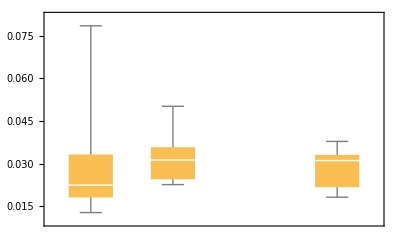

```mathematica
BoxWhiskerChart[myRNAIntensity⟦All,All,1⟧]
```

## 3. Localization-based Analysis

### 1. Plotting mean square displacement

```mathematica
myMSD=MSDcalculator[myAllParameters,10,2,0.13];
```

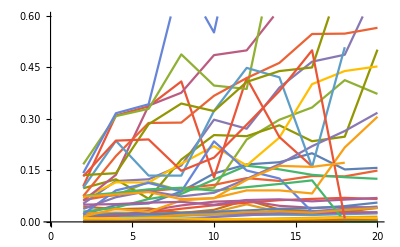
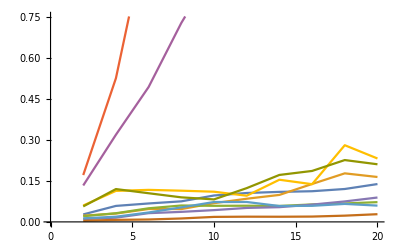
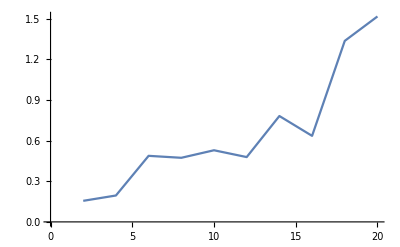
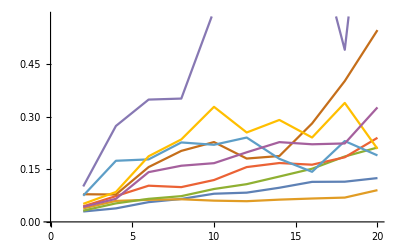

```mathematica
ListLinePlot/@myMSD⟦All,All,2,All,All,1⟧
```

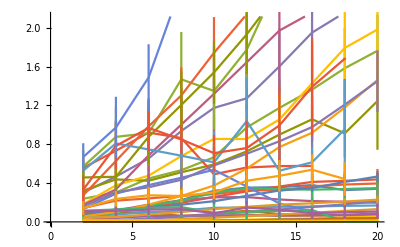
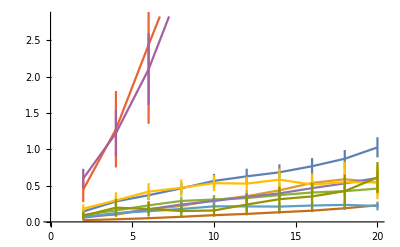
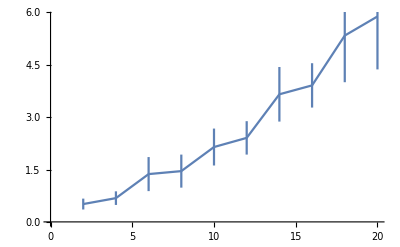
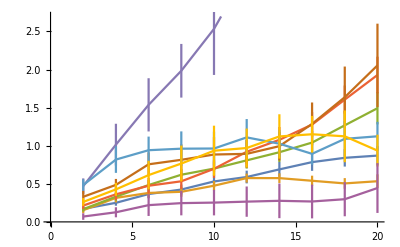

```mathematica
ErrorListPlot[#,Joined->True]&/@myMSD⟦All,All,2⟧
```

```mathematica
StandardDeviation@SplitBy[Sort@Partition[Flatten@myMSD⟦1,All,1⟧,2],First]⟦1⟧
```

{0.,0.226893}

```mathematica
Histogram@SplitBy[Sort@Partition[Flatten@myMSD⟦1,All,1⟧,2],First]⟦1⟧
```

$Aborted

```mathematica
{Mean@#,ErrorBar@((StandardDeviation@#⟦All,2⟧)/(Sqrt@Length@#))}&/@SplitBy[Sort@Partition[Flatten@#,2],First]&/@myMSD⟦All,All,1⟧
```

{{{{2,0.0899581},ErrorBar[0.00671117]},{{4,0.137031},ErrorBar[0.010779]},{{6,0.180244},ErrorBar[0.0139943]},{{8,0.222846},ErrorBar[0.0172963]},{{10,0.263202},ErrorBar[0.0209635]},{{12,0.307898},ErrorBar[0.0251827]},{{14,0.338213},ErrorBar[0.0289687]},{{16,0.367518},ErrorBar[0.0320804]},{{18,0.392276},ErrorBar[0.0352278]},{{20,0.416029},ErrorBar[0.0394056]}},{{{2,0.12187},ErrorBar[0.0135898]},{{4,0.238272},ErrorBar[0.0318136]},{{6,0.360313},ErrorBar[0.0541056]},{{8,0.48039},ErrorBar[0.0781654]},{{10,0.556493},ErrorBar[0.0911367]},{{12,0.644805},ErrorBar[0.111538]},{{14,0.706896},ErrorBar[0.120646]},{{16,0.752592},ErrorBar[0.125295]},{{18,0.802566},ErrorBar[0.136158]},{{20,0.810087},ErrorBar[0.129133]}},{{{2,0.510836},ErrorBar[0.155496]},{{4,0.680393},ErrorBar[0.194789]},{{6,1.36887},ErrorBar[0.487461]},{{8,1.45391},ErrorBar[0.47301]},{{10,2.14359},ErrorBar[0.528622]},{{12,2.40577},ErrorBar[0.478282]},{{14,3.65388},ErrorBar[0.781281]},{{16,3.9089},ErrorBar[0.634831]},{{18,5.33557},ErrorBar[1.33582]},{{20,5.88266},ErrorBar[1.51596]}},{{{2,0.235313},ErrorBar[0.0180308]},{{4,0.407823},ErrorBar[0.0322678]},{{6,0.555679},ErrorBar[0.0415691]},{{8,0.635433},ErrorBar[0.0485764]},{{10,0.73427},ErrorBar[0.057201]},{{12,0.843637},ErrorBar[0.0667171]},{{14,0.916062},ErrorBar[0.0661013]},{{16,0.974834},ErrorBar[0.0663707]},{{18,1.10647},ErrorBar[0.0780682]},{{20,1.22809},ErrorBar[0.0908255]}}}

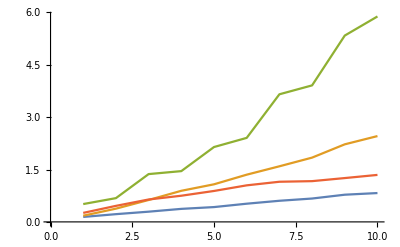

```mathematica
ListLinePlot@Table[(Mean/@SplitBy[Sort@Flatten[test⟦color,All,2⟧,1],First]),{color,1,Length@test,1}]
```

```mathematica
Table[(Mean/@SplitBy[Sort@Flatten[test⟦color,All,2⟧,1],First]),{color,1,Length@test,1}]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[{{{2,0.000507063},ErrorBar[0.0000510716]}}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{{{2,0.000841464},ErrorBar[0.000154172]}}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{{{2,0.00100583},ErrorBar[0.000307282]}}].

General::stop: Further output of Mean::rectt will be suppressed during this calculation.

{{Mean[{{{2,0.000507063},ErrorBar[0.0000510716]}}],Mean[{{{2,0.000841464},ErrorBar[0.000154172]}}],Mean[{{{2,0.00100583},ErrorBar[0.000307282]}}],Mean[{{{2,0.00104417},ErrorBar[0.000114286]}}],Mean[{{{2,0.00138366},ErrorBar[0.000261808]}}],Mean[{{{2,0.00174138},ErrorBar[0.000365304]}}],Mean[{{{2,0.00203371},ErrorBar[0.000327448]}}],Mean[{{{2,0.00205857},ErrorBar[0.000435218]}}],Mean[{{{2,0.00216711},ErrorBar[0.000380138]}}],Mean[{{{2,0.0022527},ErrorBar[0.00101474]}}],Mean[{{{2,0.00279603},ErrorBar[0.000448504]}}],Mean[{{{2,0.00447077},ErrorBar[0.000962175]}}],Mean[{{{2,0.00707372},ErrorBar[0.00107069]}}],Mean[{{{2,0.0169307},ErrorBar[0.0109243]}}],Mean[{{{2,0.020785},ErrorBar[0.0129583]}}],Mean[{{{2,0.0429952},ErrorBar[0.00847396]}}],Mean[{{{2,0.054875},ErrorBar[0.026289]}}],Mean[{{{2,0.0557285},ErrorBar[0.0167585]}}],Mean[{{{2,0.0566842},ErrorBar[0.0155285]}}],Mean[{{{2,0.0571446},ErrorBar[0.0221166]}}],Mean[{{{2,0.0602028},ErrorBar[0.0300338]}}],Mean[{{{2,0.0663872},ErrorBar[0.0145634]}}],Mean[{{{2,0.0669319},ErrorBar[0.0130089]}}],Mean[{{{2,0.0763974},ErrorBar[0.0176667]}}],Mean[{{{2,0.0980239},ErrorBar[0.0445125]}}],Mean[{{{2,0.111212},ErrorBar[0.0502836]}}],Mean[{{{2,0.115179},ErrorBar[0.0759162]}}],Mean[{{{2,0.132089},ErrorBar[0.0223589]}}],Mean[{{{2,0.141511},ErrorBar[0.0735938]}}],Mean[{{{2,0.142203},ErrorBar[0.0633367]}}],Mean[{{{2,0.161063},ErrorBar[0.0378328]}}],Mean[{{{2,0.174407},ErrorBar[0.0616443]}}],Mean[{{{2,0.183287},ErrorBar[0.068713]}}],Mean[{{{2,0.238491},ErrorBar[0.0750464]}}],Mean[{{{2,0.274012},ErrorBar[0.0750086]}}],Mean[{{{2,0.302981},ErrorBar[0.0531146]}}],Mean[{{{2,0.322408},ErrorBar[0.0979468]}}],Mean[{{{2,0.332706},ErrorBar[0.132642]}}],Mean[{{{2,0.457908},ErrorBar[0.136417]}}],Mean[{{{2,0.528918},ErrorBar[0.0993839]}}],Mean[{{{2,0.556678},ErrorBar[0.104061]}}],Mean[{{{2,0.569689},ErrorBar[0.167705]}}],Mean[{{{2,0.668767},ErrorBar[0.142207]}}],Mean[{{{4,0.000551478},ErrorBar[0.0000738721]}}],Mean[{{{4,0.00100177},ErrorBar[0.00014605]}}],Mean[{{{4,0.00101525},ErrorBar[0.000161466]}}],Mean[{{{4,0.00156248},ErrorBar[0.000228787]}}],Mean[{{{4,0.00169343},ErrorBar[0.000419822]}}],Mean[{{{4,0.00250592},ErrorBar[0.000636322]}}],Mean[{{{4,0.00302213},ErrorBar[0.000669425]}}],Mean[{{{4,0.00319654},ErrorBar[0.000709571]}}],Mean[{{{4,0.00418935},ErrorBar[0.000984585]}}],Mean[{{{4,0.0045066},ErrorBar[0.0013144]}}],Mean[{{{4,0.00575737},ErrorBar[0.000886974]}}],Mean[{{{4,0.00880724},ErrorBar[0.00134515]}}],Mean[{{{4,0.0167283},ErrorBar[0.0102132]}}],Mean[{{{4,0.0184616},ErrorBar[0.00318981]}}],Mean[{{{4,0.0409956},ErrorBar[0.0190342]}}],Mean[{{{4,0.0502166},ErrorBar[0.00912013]}}],Mean[{{{4,0.0567871},ErrorBar[0.0270013]}}],Mean[{{{4,0.0774313},ErrorBar[0.0162707]}}],Mean[{{{4,0.0927246},ErrorBar[0.0370149]}}],Mean[{{{4,0.0947368},ErrorBar[0.0415425]}}],Mean[{{{4,0.0970249},ErrorBar[0.0196226]}}],Mean[{{{4,0.102023},ErrorBar[0.0382099]}}],Mean[{{{4,0.113986},ErrorBar[0.0488215]}}],Mean[{{{4,0.114623},ErrorBar[0.0517689]}}],Mean[{{{4,0.11679},ErrorBar[0.0181416]}}],Mean[{{{4,0.127666},ErrorBar[0.0845684]}}],Mean[{{{4,0.129817},ErrorBar[0.0238523]}}],Mean[{{{4,0.219267},ErrorBar[0.0797662]}}],Mean[{{{4,0.236559},ErrorBar[0.0801788]}}],Mean[{{{4,0.291426},ErrorBar[0.0918521]}}],Mean[{{{4,0.303128},ErrorBar[0.0772665]}}],Mean[{{{4,0.305264},ErrorBar[0.071939]}}],Mean[{{{4,0.334863},ErrorBar[0.137134]}}],Mean[{{{4,0.377124},ErrorBar[0.115301]}}],Mean[{{{4,0.437827},ErrorBar[0.12412]}}],Mean[{{{4,0.464972},ErrorBar[0.141819]}}],Mean[{{{4,0.467484},ErrorBar[0.119025]}}],Mean[{{{4,0.627493},ErrorBar[0.191831]}}],Mean[{{{4,0.733217},ErrorBar[0.309944]}}],Mean[{{{4,0.783021},ErrorBar[0.236755]}}],Mean[{{{4,0.808852},ErrorBar[0.236198]}}],Mean[{{{4,0.876483},ErrorBar[0.308159]}}],Mean[{{{4,0.97296},ErrorBar[0.316609]}}],Mean[{{{6,0.000453367},ErrorBar[0.0000626089]}}],Mean[{{{6,0.00131906},ErrorBar[0.000164265]}}],Mean[{{{6,0.00132418},ErrorBar[0.000215352]}}],Mean[{{{6,0.00136287},ErrorBar[0.000188317]}}],Mean[{{{6,0.00149168},ErrorBar[0.000242441]}}],Mean[{{{6,0.0016421},ErrorBar[0.000776964]}}],Mean[{{{6,0.00530167},ErrorBar[0.00108953]}}],Mean[{{{6,0.00588258},ErrorBar[0.000983317]}}],Mean[{{{6,0.00599423},ErrorBar[0.00272486]}}],Mean[{{{6,0.00617873},ErrorBar[0.00135579]}}],Mean[{{{6,0.00682647},ErrorBar[0.00229938]}}],Mean[{{{6,0.0176523},ErrorBar[0.0111575]}}],Mean[{{{6,0.0178273},ErrorBar[0.00259299]}}],Mean[{{{6,0.034599},ErrorBar[0.00595594]}}],Mean[{{{6,0.0559757},ErrorBar[0.0266447]}}],Mean[{{{6,0.0612749},ErrorBar[0.0228117]}}],Mean[{{{6,0.0765039},ErrorBar[0.0129749]}}],Mean[{{{6,0.0974826},ErrorBar[0.016406]}}],Mean[{{{6,0.101552},ErrorBar[0.0393769]}}],Mean[{{{6,0.12598},ErrorBar[0.0561862]}}],Mean[{{{6,0.143668},ErrorBar[0.0948084]}}],Mean[{{{6,0.146292},ErrorBar[0.0226093]}}],Mean[{{{6,0.146751},ErrorBar[0.0268838]}}],Mean[{{{6,0.150419},ErrorBar[0.0536278]}}],Mean[{{{6,0.17107},ErrorBar[0.0666782]}}],Mean[{{{6,0.177564},ErrorBar[0.0290359]}}],Mean[{{{6,0.178466},ErrorBar[0.0330158]}}],Mean[{{{6,0.242103},ErrorBar[0.0898215]}}],Mean[{{{6,0.274454},ErrorBar[0.0868956]}}],Mean[{{{6,0.357113},ErrorBar[0.0901026]}}],Mean[{{{6,0.379307},ErrorBar[0.113531]}}],Mean[{{{6,0.42439},ErrorBar[0.0674348]}}],Mean[{{{6,0.447719},ErrorBar[0.117104]}}],Mean[{{{6,0.476309},ErrorBar[0.114786]}}],Mean[{{{6,0.653837},ErrorBar[0.12419]}}],Mean[{{{6,0.685829},ErrorBar[0.338703]}}],Mean[{{{6,0.746928},ErrorBar[0.134866]}}],Mean[{{{6,0.877159},ErrorBar[0.284542]}}],Mean[{{{6,0.914197},ErrorBar[0.329479]}}],Mean[{{{6,0.921084},ErrorBar[0.336682]}}],Mean[{{{6,0.968864},ErrorBar[0.240233]}}],Mean[{{{6,0.985179},ErrorBar[0.288275]}}],Mean[{{{6,1.48844},ErrorBar[0.342683]}}],Mean[{{{8,0.000536308},ErrorBar[0.0000697008]}}],Mean[{{{8,0.00147463},ErrorBar[0.000196547]}}],Mean[{{{8,0.0015451},ErrorBar[0.000483338]}}],Mean[{{{8,0.00163763},ErrorBar[0.000396777]}}],Mean[{{{8,0.00189361},ErrorBar[0.000264889]}}],Mean[{{{8,0.00291641},ErrorBar[0.00096615]}}],Mean[{{{8,0.00773556},ErrorBar[0.0033607]}}],Mean[{{{8,0.00858615},ErrorBar[0.00167921]}}],Mean[{{{8,0.0087763},ErrorBar[0.00251054]}}],Mean[{{{8,0.0090912},ErrorBar[0.00314805]}}],Mean[{{{8,0.00961942},ErrorBar[0.00122285]}}],Mean[{{{8,0.0169299},ErrorBar[0.0107813]}}],Mean[{{{8,0.0293894},ErrorBar[0.00392348]}}],Mean[{{{8,0.0542859},ErrorBar[0.00945573]}}],Mean[{{{8,0.0585672},ErrorBar[0.0278666]}}],Mean[{{{8,0.0600527},ErrorBar[0.0259962]}}],Mean[{{{8,0.0633452},ErrorBar[0.023675]}}],Mean[{{{8,0.101846},ErrorBar[0.0204356]}}],Mean[{{{8,0.116887},ErrorBar[0.0179472]}}],Mean[{{{8,0.131737},ErrorBar[0.0583807]}}],Mean[{{{8,0.152058},ErrorBar[0.0995085]}}],Mean[{{{8,0.177458},ErrorBar[0.0259472]}}],Mean[{{{8,0.196463},ErrorBar[0.0383928]}}],Mean[{{{8,0.217417},ErrorBar[0.0814663]}}],Mean[{{{8,0.221703},ErrorBar[0.0479721]}}],Mean[{{{8,0.224549},ErrorBar[0.0887593]}}],Mean[{{{8,0.266435},ErrorBar[0.0662517]}}],Mean[{{{8,0.267326},ErrorBar[0.0623161]}}],Mean[{{{8,0.269404},ErrorBar[0.0978645]}}],Mean[{{{8,0.433939},ErrorBar[0.0743113]}}],Mean[{{{8,0.454701},ErrorBar[0.0887426]}}],Mean[{{{8,0.511351},ErrorBar[0.181627]}}],Mean[{{{8,0.532794},ErrorBar[0.0908083]}}],Mean[{{{8,0.678876},ErrorBar[0.169572]}}],Mean[{{{8,0.682308},ErrorBar[0.134824]}}],Mean[{{{8,0.849755},ErrorBar[0.148905]}}],Mean[{{{8,0.864613},ErrorBar[0.40918]}}],Mean[{{{8,0.937527},ErrorBar[0.164389]}}],Mean[{{{8,1.0027},ErrorBar[0.376306]}}],Mean[{{{8,1.20554},ErrorBar[0.344825]}}],Mean[{{{8,1.30328},ErrorBar[0.289274]}}],Mean[{{{8,1.46925},ErrorBar[0.488069]}}],Mean[{{{8,2.42981},ErrorBar[0.720509]}}],Mean[{{{10,0.000652354},ErrorBar[0.0000986785]}}],Mean[{{{10,0.00149464},ErrorBar[0.000183896]}}],Mean[{{{10,0.00163852},ErrorBar[0.000213411]}}],Mean[{{{10,0.00168815},ErrorBar[0.000274573]}}],Mean[{{{10,0.00205528},ErrorBar[0.000393982]}}],Mean[{{{10,0.00228351},ErrorBar[0.000591621]}}],Mean[{{{10,0.00803452},ErrorBar[0.00290308]}}],Mean[{{{10,0.00826118},ErrorBar[0.00273451]}}],Mean[{{{10,0.00933932},ErrorBar[0.00750373]}}],Mean[{{{10,0.0112814},ErrorBar[0.00171861]}}],Mean[{{{10,0.0118446},ErrorBar[0.00210466]}}],Mean[{{{10,0.0149608},ErrorBar[0.00171248]}}],Mean[{{{10,0.0430751},ErrorBar[0.00555697]}}],Mean[{{{10,0.0587841},ErrorBar[0.0281277]}}],Mean[{{{10,0.0654749},ErrorBar[0.0245253]}}],Mean[{{{10,0.0773848},ErrorBar[0.0141392]}}],Mean[{{{10,0.0827028},ErrorBar[0.0351311]}}],Mean[{{{10,0.0889136},ErrorBar[0.0498718]}}],Mean[{{{10,0.0942924},ErrorBar[0.0910633]}}],Mean[{{{10,0.132068},ErrorBar[0.0221608]}}],Mean[{{{10,0.144988},ErrorBar[0.0213811]}}],Mean[{{{10,0.213334},ErrorBar[0.0291777]}}],Mean[{{{10,0.25342},ErrorBar[0.0589393]}}],Mean[{{{10,0.257456},ErrorBar[0.0483492]}}],Mean[{{{10,0.285732},ErrorBar[0.107819]}}],Mean[{{{10,0.300818},ErrorBar[0.123247]}}],Mean[{{{10,0.304019},ErrorBar[0.0692384]}}],Mean[{{{10,0.320585},ErrorBar[0.141145]}}],Mean[{{{10,0.37432},ErrorBar[0.0692222]}}],Mean[{{{10,0.490676},ErrorBar[0.129456]}}],Mean[{{{10,0.536916},ErrorBar[0.234648]}}],Mean[{{{10,0.581657},ErrorBar[0.0848307]}}],Mean[{{{10,0.591798},ErrorBar[0.252918]}}],Mean[{{{10,0.614157},ErrorBar[0.323427]}}],Mean[{{{10,0.665818},ErrorBar[0.0996667]}}],Mean[{{{10,0.708762},ErrorBar[0.18723]}}],Mean[{{{10,0.855021},ErrorBar[0.2207]}}],Mean[{{{10,1.17521},ErrorBar[0.297824]}}],Mean[{{{10,1.32035},ErrorBar[0.485874]}}],Mean[{{{10,1.34988},ErrorBar[0.397212]}}],Mean[{{{10,1.54061},ErrorBar[0.322838]}}],Mean[{{{10,1.74323},ErrorBar[0.36742]}}],Mean[{{{10,2.90009},ErrorBar[0.551937]}}],Mean[{{{12,0.000571051},ErrorBar[0.000093931]}}],Mean[{{{12,0.00125081},ErrorBar[0.000379961]}}],Mean[{{{12,0.00149499},ErrorBar[0.000202721]}}],Mean[{{{12,0.00181849},ErrorBar[0.000253433]}}],Mean[{{{12,0.00184117},ErrorBar[0.000850383]}}],Mean[{{{12,0.00245611},ErrorBar[0.000405785]}}],Mean[{{{12,0.0082113},ErrorBar[0.00357609]}}],Mean[{{{12,0.00936914},ErrorBar[0.00315818]}}],Mean[{{{12,0.0101339},ErrorBar[0.00856513]}}],Mean[{{{12,0.0163913},ErrorBar[0.00294732]}}],Mean[{{{12,0.0173083},ErrorBar[0.0032711]}}],Mean[{{{12,0.0228812},ErrorBar[0.00229176]}}],Mean[{{{12,0.058401},ErrorBar[0.00757064]}}],Mean[{{{12,0.0675819},ErrorBar[0.0253084]}}],Mean[{{{12,0.0785885},ErrorBar[0.0511663]}}],Mean[{{{12,0.102607},ErrorBar[0.0192871]}}],Mean[{{{12,0.102793},ErrorBar[0.101235]}}],Mean[{{{12,0.115628},ErrorBar[0.0638767]}}],Mean[{{{12,0.147619},ErrorBar[0.0636969]}}],Mean[{{{12,0.148993},ErrorBar[0.0203788]}}],Mean[{{{12,0.155586},ErrorBar[0.0284047]}}],Mean[{{{12,0.255529},ErrorBar[0.0619953]}}],Mean[{{{12,0.267941},ErrorBar[0.0333476]}}],Mean[{{{12,0.314557},ErrorBar[0.05589]}}],Mean[{{{12,0.326789},ErrorBar[0.1276]}}],Mean[{{{12,0.346551},ErrorBar[0.163681]}}],Mean[{{{12,0.352816},ErrorBar[0.167336]}}],Mean[{{{12,0.365274},ErrorBar[0.149796]}}],Mean[{{{12,0.423472},ErrorBar[0.122639]}}],Mean[{{{12,0.549032},ErrorBar[0.0917194]}}],Mean[{{{12,0.560564},ErrorBar[0.419366]}}],Mean[{{{12,0.702484},ErrorBar[0.125371]}}],Mean[{{{12,0.726948},ErrorBar[0.249785]}}],Mean[{{{12,0.760944},ErrorBar[0.283225]}}],Mean[{{{12,0.854468},ErrorBar[0.164392]}}],Mean[{{{12,0.973326},ErrorBar[0.240117]}}],Mean[{{{12,1.03873},ErrorBar[0.448692]}}],Mean[{{{12,1.2737},ErrorBar[0.271496]}}],Mean[{{{12,1.64497},ErrorBar[0.499706]}}],Mean[{{{12,1.77382},ErrorBar[0.387375]}}],Mean[{{{12,1.93231},ErrorBar[0.407762]}}],Mean[{{{12,2.14001},ErrorBar[0.419102]}}],Mean[{{{12,3.7469},ErrorBar[0.984692]}}],Mean[{{{14,0.00069615},ErrorBar[0.000100265]}}],Mean[{{{14,0.00131976},ErrorBar[0.000160038]}}],Mean[{{{14,0.00152308},ErrorBar[0.000412287]}}],Mean[{{{14,0.00162844},ErrorBar[0.000517088]}}],Mean[{{{14,0.00173924},ErrorBar[0.000314071]}}],Mean[{{{14,0.00272723},ErrorBar[0.000490788]}}],Mean[{{{14,0.00687935},ErrorBar[0.00382291]}}],Mean[{{{14,0.00938364},ErrorBar[0.00271354]}}],Mean[{{{14,0.0103536},ErrorBar[0.00874996]}}],Mean[{{{14,0.0216073},ErrorBar[0.00421042]}}],Mean[{{{14,0.0232855},ErrorBar[0.00489838]}}],Mean[{{{14,0.0307322},ErrorBar[0.00287986]}}],Mean[{{{14,0.0612201},ErrorBar[0.0290449]}}],Mean[{{{14,0.0656544},ErrorBar[0.0247864]}}],Mean[{{{14,0.0759001},ErrorBar[0.00999088]}}],Mean[{{{14,0.0797563},ErrorBar[0.0358903]}}],Mean[{{{14,0.112278},ErrorBar[0.110507]}}],Mean[{{{14,0.126329},ErrorBar[0.0657523]}}],Mean[{{{14,0.127268},ErrorBar[0.02479]}}],Mean[{{{14,0.1559},ErrorBar[0.0208933]}}],Mean[{{{14,0.177664},ErrorBar[0.0309919]}}],Mean[{{{14,0.191026},ErrorBar[0.126487]}}],Mean[{{{14,0.230719},ErrorBar[0.0468376]}}],Mean[{{{14,0.323492},ErrorBar[0.0383239]}}],Mean[{{{14,0.323659},ErrorBar[0.119244]}}],Mean[{{{14,0.33762},ErrorBar[0.153077]}}],Mean[{{{14,0.357729},ErrorBar[0.173864]}}],Mean[{{{14,0.364453},ErrorBar[0.0632399]}}],Mean[{{{14,0.474877},ErrorBar[0.163242]}}],Mean[{{{14,0.527494},ErrorBar[0.421205]}}],Mean[{{{14,0.575405},ErrorBar[0.24716]}}],Mean[{{{14,0.771356},ErrorBar[0.0918133]}}],Mean[{{{14,0.830712},ErrorBar[0.168056]}}],Mean[{{{14,0.899472},ErrorBar[0.281436]}}],Mean[{{{14,0.994071},ErrorBar[0.38122]}}],Mean[{{{14,1.05567},ErrorBar[0.245594]}}],Mean[{{{14,1.17459},ErrorBar[0.297624]}}],Mean[{{{14,1.60254},ErrorBar[0.391206]}}],Mean[{{{14,1.97222},ErrorBar[0.619947]}}],Mean[{{{14,2.37279},ErrorBar[0.439411]}}],Mean[{{{14,2.43345},ErrorBar[0.463262]}}],Mean[{{{14,2.50131},ErrorBar[0.841543]}}],Mean[{{{14,4.5958},ErrorBar[1.71864]}}],Mean[{{{16,0.000769221},ErrorBar[0.000108555]}}],Mean[{{{16,0.00144878},ErrorBar[0.000218964]}}],Mean[{{{16,0.00195778},ErrorBar[0.000311415]}}],Mean[{{{16,0.00246469},ErrorBar[0.000739469]}}],Mean[{{{16,0.00266276},ErrorBar[0.00125836]}}],Mean[{{{16,0.00310443},ErrorBar[0.000564012]}}],Mean[{{{16,0.00447654},ErrorBar[0.000888019]}}],Mean[{{{16,0.0106666},ErrorBar[0.00307326]}}],Mean[{{{16,0.0115845},ErrorBar[0.0098899]}}],Mean[{{{16,0.0266997},ErrorBar[0.00505535]}}],Mean[{{{16,0.0298847},ErrorBar[0.00817025]}}],Mean[{{{16,0.0361829},ErrorBar[0.00339251]}}],Mean[{{{16,0.0627884},ErrorBar[0.0295512]}}],Mean[{{{16,0.0677471},ErrorBar[0.0254396]}}],Mean[{{{16,0.0761143},ErrorBar[0.0312981]}}],Mean[{{{16,0.0906834},ErrorBar[0.0599232]}}],Mean[{{{16,0.094044},ErrorBar[0.0120746]}}],Mean[{{{16,0.103094},ErrorBar[0.0292979]}}],Mean[{{{16,0.12236},ErrorBar[0.120951]}}],Mean[{{{16,0.153987},ErrorBar[0.030786]}}],Mean[{{{16,0.158587},ErrorBar[0.0201593]}}],Mean[{{{16,0.191976},ErrorBar[0.0268486]}}],Mean[{{{16,0.214493},ErrorBar[0.0410035]}}],Mean[{{{16,0.332375},ErrorBar[0.137124]}}],Mean[{{{16,0.348663},ErrorBar[0.0397754]}}],Mean[{{{16,0.366346},ErrorBar[0.133693]}}],Mean[{{{16,0.379664},ErrorBar[0.199994]}}],Mean[{{{16,0.411978},ErrorBar[0.0669824]}}],Mean[{{{16,0.537589},ErrorBar[0.160314]}}],Mean[{{{16,0.577261},ErrorBar[0.161736]}}],Mean[{{{16,0.614667},ErrorBar[0.159816]}}],Mean[{{{16,0.918856},ErrorBar[0.0828992]}}],Mean[{{{16,0.97749},ErrorBar[0.220563]}}],Mean[{{{16,1.05727},ErrorBar[0.235063]}}],Mean[{{{16,1.36363},ErrorBar[0.333371]}}],Mean[{{{16,1.39264},ErrorBar[0.499875]}}],Mean[{{{16,1.42808},ErrorBar[0.401306]}}],Mean[{{{16,1.9512},ErrorBar[0.466777]}}],Mean[{{{16,2.15788},ErrorBar[0.703118]}}],Mean[{{{16,2.51143},ErrorBar[1.19698]}}],Mean[{{{16,2.79043},ErrorBar[0.547434]}}],Mean[{{{16,2.86811},ErrorBar[0.449972]}}],Mean[{{{16,4.31726},ErrorBar[1.85849]}}],Mean[{{{18,0.000616444},ErrorBar[0.0000951399]}}],Mean[{{{18,0.00135331},ErrorBar[0.00016207]}}],Mean[{{{18,0.00172838},ErrorBar[0.000290065]}}],Mean[{{{18,0.00206586},ErrorBar[0.000283887]}}],Mean[{{{18,0.00207588},ErrorBar[0.00122606]}}],Mean[{{{18,0.00247508},ErrorBar[0.00120337]}}],Mean[{{{18,0.0033255},ErrorBar[0.000604946]}}],Mean[{{{18,0.0137498},ErrorBar[0.0126873]}}],Mean[{{{18,0.0157577},ErrorBar[0.00474546]}}],Mean[{{{18,0.0324531},ErrorBar[0.00618214]}}],Mean[{{{18,0.0352176},ErrorBar[0.0122141]}}],Mean[{{{18,0.0434987},ErrorBar[0.00343148]}}],Mean[{{{18,0.0664172},ErrorBar[0.031271]}}],Mean[{{{18,0.0705414},ErrorBar[0.0265994]}}],Mean[{{{18,0.0731728},ErrorBar[0.02869]}}],Mean[{{{18,0.099468},ErrorBar[0.0649251]}}],Mean[{{{18,0.113313},ErrorBar[0.0140029]}}],Mean[{{{18,0.165625},ErrorBar[0.0225444]}}],Mean[{{{18,0.182075},ErrorBar[0.0381163]}}],Mean[{{{18,0.207728},ErrorBar[0.0433357]}}],Mean[{{{18,0.209212},ErrorBar[0.0349579]}}],Mean[{{{18,0.327474},ErrorBar[0.152823]}}],Mean[{{{18,0.338967},ErrorBar[0.130204]}}],Mean[{{{18,0.385027},ErrorBar[0.132633]}}],Mean[{{{18,0.412176},ErrorBar[0.0459833]}}],Mean[{{{18,0.423445},ErrorBar[0.0700453]}}],Mean[{{{18,0.442296},ErrorBar[0.172476]}}],Mean[{{{18,0.912865},ErrorBar[0.248232]}}],Mean[{{{18,0.955107},ErrorBar[0.508937]}}],Mean[{{{18,1.17908},ErrorBar[0.217023]}}],Mean[{{{18,1.20863},ErrorBar[0.264854]}}],Mean[{{{18,1.58416},ErrorBar[0.412954]}}],Mean[{{{18,1.68218},ErrorBar[0.0101838]}}],Mean[{{{18,1.793},ErrorBar[0.439595]}}],Mean[{{{18,2.15804},ErrorBar[0.487102]}}],Mean[{{{18,3.15162},ErrorBar[0.548489]}}],Mean[{{{18,3.69067},ErrorBar[0.736637]}}],Mean[{{{18,5.48533},ErrorBar[1.93424]}}],Mean[{{{20,0.000709314},ErrorBar[0.000121494]}}],Mean[{{{20,0.00100409},ErrorBar[0.000578204]}}],Mean[{{{20,0.00144958},ErrorBar[0.000616132]}}],Mean[{{{20,0.00159105},ErrorBar[0.000208234]}}],Mean[{{{20,0.00161511},ErrorBar[0.00029751]}}],Mean[{{{20,0.00171463},ErrorBar[0.00118028]}}],Mean[{{{20,0.00347939},ErrorBar[0.00054414]}}],Mean[{{{20,0.0111555},ErrorBar[0.0034428]}}],Mean[{{{20,0.0116518},ErrorBar[0.0110842]}}],Mean[{{{20,0.0380008},ErrorBar[0.00685632]}}],Mean[{{{20,0.0381407},ErrorBar[0.00682262]}}],Mean[{{{20,0.0479072},ErrorBar[0.0262299]}}],Mean[{{{20,0.0538661},ErrorBar[0.00272321]}}],Mean[{{{20,0.0763988},ErrorBar[0.0283237]}}],Mean[{{{20,0.0867713},ErrorBar[0.0410599]}}],Mean[{{{20,0.106803},ErrorBar[0.0698475]}}],Mean[{{{20,0.131488},ErrorBar[0.0151903]}}],Mean[{{{20,0.168928},ErrorBar[0.0247793]}}],Mean[{{{20,0.197449},ErrorBar[0.0420456]}}],Mean[{{{20,0.210246},ErrorBar[0.0446304]}}],Mean[{{{20,0.229338},ErrorBar[0.0404086]}}],Mean[{{{20,0.341141},ErrorBar[0.157419]}}],Mean[{{{20,0.348607},ErrorBar[0.125551]}}],Mean[{{{20,0.396073},ErrorBar[0.149502]}}],Mean[{{{20,0.437799},ErrorBar[0.0666737]}}],Mean[{{{20,0.467688},ErrorBar[0.0562605]}}],Mean[{{{20,1.24555},ErrorBar[0.501799]}}],Mean[{{{20,1.45054},ErrorBar[0.317978]}}],Mean[{{{20,1.46213},ErrorBar[0.306282]}}],Mean[{{{20,1.7635},ErrorBar[0.372878]}}],Mean[{{{20,1.98313},ErrorBar[0.452936]}}],Mean[{{{20,2.53391},ErrorBar[0.689978]}}],Mean[{{{20,3.53417},ErrorBar[0.56544]}}],Mean[{{{20,4.91725},ErrorBar[0.992343]}}]},{Mean[{{{2,0.0229601},ErrorBar[0.00419612]}}],Mean[{{{2,0.0588537},ErrorBar[0.0103601]}}],Mean[{{{2,0.0690999},ErrorBar[0.0130749]}}],Mean[{{{2,0.07704},ErrorBar[0.0227539]}}],Mean[{{{2,0.0841264},ErrorBar[0.056657]}}],Mean[{{{2,0.0955178},ErrorBar[0.020834]}}],Mean[{{{2,0.143408},ErrorBar[0.027342]}}],Mean[{{{2,0.181489},ErrorBar[0.0598984]}}],Mean[{{{2,0.444244},ErrorBar[0.171299]}}],Mean[{{{2,0.596833},ErrorBar[0.133216]}}],Mean[{{{4,0.0360396},ErrorBar[0.00741699]}}],Mean[{{{4,0.0990892},ErrorBar[0.0304546]}}],Mean[{{{4,0.109717},ErrorBar[0.0154751]}}],Mean[{{{4,0.120812},ErrorBar[0.0190004]}}],Mean[{{{4,0.158074},ErrorBar[0.0317108]}}],Mean[{{{4,0.195396},ErrorBar[0.120071]}}],Mean[{{{4,0.281763},ErrorBar[0.0584783]}}],Mean[{{{4,0.2954},ErrorBar[0.113436]}}],Mean[{{{4,1.22055},ErrorBar[0.318821]}}],Mean[{{{4,1.27495},ErrorBar[0.525507]}}],Mean[{{{6,0.0507326},ErrorBar[0.00875261]}}],Mean[{{{6,0.147274},ErrorBar[0.0344431]}}],Mean[{{{6,0.173484},ErrorBar[0.0319256]}}],Mean[{{{6,0.174871},ErrorBar[0.0471106]}}],Mean[{{{6,0.178697},ErrorBar[0.104801]}}],Mean[{{{6,0.227489},ErrorBar[0.0497338]}}],Mean[{{{6,0.367119},ErrorBar[0.0674193]}}],Mean[{{{6,0.416255},ErrorBar[0.117108]}}],Mean[{{{6,2.1003},ErrorBar[0.493342]}}],Mean[{{{6,2.43711},ErrorBar[1.08711]}}],Mean[{{{8,0.0702214},ErrorBar[0.0125103]}}],Mean[{{{8,0.149619},ErrorBar[0.0897876]}}],Mean[{{{8,0.177634},ErrorBar[0.0531165]}}],Mean[{{{8,0.218687},ErrorBar[0.0469316]}}],Mean[{{{8,0.239179},ErrorBar[0.0366781]}}],Mean[{{{8,0.288188},ErrorBar[0.0599619]}}],Mean[{{{8,0.462025},ErrorBar[0.0751734]}}],Mean[{{{8,0.469567},ErrorBar[0.114123]}}],Mean[{{{8,3.25954},ErrorBar[0.727602]}}],Mean[{{{8,3.56934},ErrorBar[1.74316]}}],Mean[{{{10,0.0928254},ErrorBar[0.0182953]}}],Mean[{{{10,0.157008},ErrorBar[0.0822974]}}],Mean[{{{10,0.214354},ErrorBar[0.0726919]}}],Mean[{{{10,0.287317},ErrorBar[0.0430631]}}],Mean[{{{10,0.298977},ErrorBar[0.0684634]}}],Mean[{{{10,0.308203},ErrorBar[0.0588249]}}],Mean[{{{10,0.533004},ErrorBar[0.110417]}}],Mean[{{{10,0.563822},ErrorBar[0.0965552]}}],Mean[{{{10,3.89307},ErrorBar[0.926765]}}],Mean[{{{10,4.41459},ErrorBar[2.15984]}}],Mean[{{{12,0.109676},ErrorBar[0.0190811]}}],Mean[{{{12,0.213126},ErrorBar[0.072844]}}],Mean[{{{12,0.238819},ErrorBar[0.1235]}}],Mean[{{{12,0.32797},ErrorBar[0.0591262]}}],Mean[{{{12,0.343214},ErrorBar[0.05108]}}],Mean[{{{12,0.354106},ErrorBar[0.0847121]}}],Mean[{{{12,0.527006},ErrorBar[0.0957155]}}],Mean[{{{12,0.626625},ErrorBar[0.105681]}}],Mean[{{{12,5.33312},ErrorBar[1.39857]}}],Mean[{{{12,5.44598},ErrorBar[2.64949]}}],Mean[{{{14,0.132899},ErrorBar[0.0188597]}}],Mean[{{{14,0.210555},ErrorBar[0.0580796]}}],Mean[{{{14,0.312299},ErrorBar[0.171733]}}],Mean[{{{14,0.368535},ErrorBar[0.0583282]}}],Mean[{{{14,0.392142},ErrorBar[0.0538535]}}],Mean[{{{14,0.434305},ErrorBar[0.0986784]}}],Mean[{{{14,0.581669},ErrorBar[0.154211]}}],Mean[{{{14,0.682261},ErrorBar[0.109789]}}],Mean[{{{14,6.27922},ErrorBar[1.76443]}}],Mean[{{{14,6.5253},ErrorBar[2.74263]}}],Mean[{{{16,0.154483},ErrorBar[0.0194732]}}],Mean[{{{16,0.225027},ErrorBar[0.0587535]}}],Mean[{{{16,0.350496},ErrorBar[0.18634]}}],Mean[{{{16,0.404314},ErrorBar[0.0638447]}}],Mean[{{{16,0.464588},ErrorBar[0.0632056]}}],Mean[{{{16,0.513884},ErrorBar[0.13791]}}],Mean[{{{16,0.536364},ErrorBar[0.138647]}}],Mean[{{{16,0.765985},ErrorBar[0.112182]}}],Mean[{{{16,6.49718},ErrorBar[1.96503]}}],Mean[{{{16,8.49362},ErrorBar[2.86156]}}],Mean[{{{18,0.187535},ErrorBar[0.0228288]}}],Mean[{{{18,0.23457},ErrorBar[0.0657757]}}],Mean[{{{18,0.423085},ErrorBar[0.0674664]}}],Mean[{{{18,0.423236},ErrorBar[0.226138]}}],Mean[{{{18,0.529856},ErrorBar[0.0748476]}}],Mean[{{{18,0.54657},ErrorBar[0.280427]}}],Mean[{{{18,0.58696},ErrorBar[0.177551]}}],Mean[{{{18,0.868962},ErrorBar[0.120328]}}],Mean[{{{18,6.9362},ErrorBar[2.10314]}}],Mean[{{{18,11.4754},ErrorBar[3.76622]}}],Mean[{{{20,0.218682},ErrorBar[0.0595636]}}],Mean[{{{20,0.228421},ErrorBar[0.0281575]}}],Mean[{{{20,0.458323},ErrorBar[0.0722529]}}],Mean[{{{20,0.542598},ErrorBar[0.231941]}}],Mean[{{{20,0.54407},ErrorBar[0.164222]}}],Mean[{{{20,0.604168},ErrorBar[0.0891508]}}],Mean[{{{20,0.612207},ErrorBar[0.210753]}}],Mean[{{{20,1.02539},ErrorBar[0.138396]}}],Mean[{{{20,6.84426},ErrorBar[2.05541]}}],Mean[{{{20,13.4956},ErrorBar[4.1503]}}]},{Mean[{{{2,0.510836},ErrorBar[0.155496]}}],Mean[{{{4,0.680393},ErrorBar[0.194789]}}],Mean[{{{6,1.36887},ErrorBar[0.487461]}}],Mean[{{{8,1.45391},ErrorBar[0.47301]}}],Mean[{{{10,2.14359},ErrorBar[0.528622]}}],Mean[{{{12,2.40577},ErrorBar[0.478282]}}],Mean[{{{14,3.65388},ErrorBar[0.781281]}}],Mean[{{{16,3.9089},ErrorBar[0.634831]}}],Mean[{{{18,5.33557},ErrorBar[1.33582]}}],Mean[{{{20,5.88266},ErrorBar[1.51596]}}]},{Mean[{{{2,0.070241},ErrorBar[0.0429369]}}],Mean[{{{2,0.153664},ErrorBar[0.0385458]}}],Mean[{{{2,0.167207},ErrorBar[0.0321116]}}],Mean[{{{2,0.171011},ErrorBar[0.0297178]}}],Mean[{{{2,0.214683},ErrorBar[0.0443458]}}],Mean[{{{2,0.261818},ErrorBar[0.051506]}}],Mean[{{{2,0.329642},ErrorBar[0.0789928]}}],Mean[{{{2,0.469909},ErrorBar[0.101238]}}],Mean[{{{2,0.48413},ErrorBar[0.0749015]}}],Mean[{{{4,0.126268},ErrorBar[0.0659486]}}],Mean[{{{4,0.250602},ErrorBar[0.0385917]}}],Mean[{{{4,0.315201},ErrorBar[0.0599696]}}],Mean[{{{4,0.331589},ErrorBar[0.0529239]}}],Mean[{{{4,0.362171},ErrorBar[0.0736159]}}],Mean[{{{4,0.426933},ErrorBar[0.0854573]}}],Mean[{{{4,0.486071},ErrorBar[0.0781519]}}],Mean[{{{4,0.818358},ErrorBar[0.17459]}}],Mean[{{{4,1.01437},ErrorBar[0.274044]}}],Mean[{{{6,0.22009},ErrorBar[0.142134]}}],Mean[{{{6,0.365623},ErrorBar[0.0564349]}}],Mean[{{{6,0.380097},ErrorBar[0.0630447]}}],Mean[{{{6,0.474551},ErrorBar[0.103412]}}],Mean[{{{6,0.484192},ErrorBar[0.0658588]}}],Mean[{{{6,0.614468},ErrorBar[0.187446]}}],Mean[{{{6,0.756144},ErrorBar[0.156583]}}],Mean[{{{6,0.941248},ErrorBar[0.178544]}}],Mean[{{{6,1.53683},ErrorBar[0.349355]}}],Mean[{{{8,0.24649},ErrorBar[0.160434]}}],Mean[{{{8,0.395238},ErrorBar[0.064652]}}],Mean[{{{8,0.424763},ErrorBar[0.0655384]}}],Mean[{{{8,0.533061},ErrorBar[0.0993318]}}],Mean[{{{8,0.619187},ErrorBar[0.0735593]}}],Mean[{{{8,0.766131},ErrorBar[0.235556]}}],Mean[{{{8,0.815071},ErrorBar[0.202857]}}],Mean[{{{8,0.961229},ErrorBar[0.226935]}}],Mean[{{{8,1.98425},ErrorBar[0.352258]}}],Mean[{{{10,0.253384},ErrorBar[0.167737]}}],Mean[{{{10,0.475227},ErrorBar[0.0607021]}}],Mean[{{{10,0.53112},ErrorBar[0.0804709]}}],Mean[{{{10,0.696607},ErrorBar[0.11959]}}],Mean[{{{10,0.699848},ErrorBar[0.0939693]}}],Mean[{{{10,0.884585},ErrorBar[0.227991]}}],Mean[{{{10,0.934528},ErrorBar[0.328653]}}],Mean[{{{10,0.963419},ErrorBar[0.220254]}}],Mean[{{{10,2.53376},ErrorBar[0.604334]}}],Mean[{{{12,0.266083},ErrorBar[0.198814]}}],Mean[{{{12,0.57532},ErrorBar[0.0591111]}}],Mean[{{{12,0.589185},ErrorBar[0.0835356]}}],Mean[{{{12,0.807834},ErrorBar[0.107794]}}],Mean[{{{12,0.893325},ErrorBar[0.180953]}}],Mean[{{{12,0.920531},ErrorBar[0.156593]}}],Mean[{{{12,0.969952},ErrorBar[0.255376]}}],Mean[{{{12,1.10942},ErrorBar[0.240942]}}],Mean[{{{12,3.28697},ErrorBar[1.1643]}}],Mean[{{{14,0.276814},ErrorBar[0.227837]}}],Mean[{{{14,0.5747},ErrorBar[0.0635868]}}],Mean[{{{14,0.689383},ErrorBar[0.0975592]}}],Mean[{{{14,0.914693},ErrorBar[0.129629]}}],Mean[{{{14,0.994268},ErrorBar[0.188183]}}],Mean[{{{14,1.02654},ErrorBar[0.180128]}}],Mean[{{{14,1.07759},ErrorBar[0.168143]}}],Mean[{{{14,1.12195},ErrorBar[0.291187]}}],Mean[{{{14,3.66936},ErrorBar[0.983379]}}],Mean[{{{16,0.267901},ErrorBar[0.221693]}}],Mean[{{{16,0.539989},ErrorBar[0.0667837]}}],Mean[{{{16,0.784823},ErrorBar[0.114346]}}],Mean[{{{16,0.893517},ErrorBar[0.143092]}}],Mean[{{{16,1.04133},ErrorBar[0.151838]}}],Mean[{{{16,1.1506},ErrorBar[0.241027]}}],Mean[{{{16,1.27734},ErrorBar[0.163384]}}],Mean[{{{16,1.28649},ErrorBar[0.281217]}}],Mean[{{{16,3.26021},ErrorBar[0.8473]}}],Mean[{{{18,0.297904},ErrorBar[0.224065]}}],Mean[{{{18,0.505293},ErrorBar[0.0694496]}}],Mean[{{{18,0.841209},ErrorBar[0.114815]}}],Mean[{{{18,1.09029},ErrorBar[0.230906]}}],Mean[{{{18,1.12359},ErrorBar[0.33984]}}],Mean[{{{18,1.26802},ErrorBar[0.18684]}}],Mean[{{{18,1.60588},ErrorBar[0.184622]}}],Mean[{{{18,1.63721},ErrorBar[0.402329]}}],Mean[{{{18,2.92567},ErrorBar[0.491614]}}],Mean[{{{20,0.444753},ErrorBar[0.32701]}}],Mean[{{{20,0.533894},ErrorBar[0.0906846]}}],Mean[{{{20,0.870297},ErrorBar[0.125122]}}],Mean[{{{20,0.936054},ErrorBar[0.20875]}}],Mean[{{{20,1.12373},ErrorBar[0.189911]}}],Mean[{{{20,1.49249},ErrorBar[0.212408]}}],Mean[{{{20,1.92864},ErrorBar[0.240181]}}],Mean[{{{20,2.05472},ErrorBar[0.547788]}}],Mean[{{{20,2.72478},ErrorBar[1.3035]}}]}}